```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/oernst/Research/cnl/dynamic_boltzmann_cpp/helix/split

Params

```mathematica
dir="data_learned_split/";
```

### N opt steps

```mathematica
nOpt=400;
```

### Time

```mathematica
tGrid=Flatten[Import[dir<>"grid_time.txt","Table"]];
nt=Length[tGrid];
tmax=tGrid[[-1]];
```

### Space

```mathematica
{nuMinMax["hA"],nuMinMax["hB"]}=Transpose[Import[dir<>"grid_F_hA.txt","Table"]][[;;,{1,-1}]];
```

### Moments

```mathematica
momsMinMax=Association[];
momsMinMax["hA"]={0,300};
momsMinMax["hB"]={0,300};
momsMinMax["hC"]={0,300};
```

Moments

```mathematica
pts={};
Do[
AppendTo[pts,{}];
Do[
latt=Import["stoch_sim_"<>ToString[idx]<>"/lattice_v001/lattice/"<>IntegerString[i,10,4]<>".txt","Table"];
nA=Length[Select[latt,#[[2]]=="A"&]];
nB=Length[Select[latt,#[[2]]=="B"&]];
nC=Length[Select[latt,#[[2]]=="C"&]];
AppendTo[pts[[idx]],{nA,nB,nC}];
,{i,0,24}];
,{idx,1,8}];
```

```mathematica
ListPointPlot3D[pts]/.Point->Line
```

-Graphics3D-

Moments dynamic

```mathematica
Manipulate[
Quiet[Check[
fmhA={};
fmhB={};
fmhC={};
Do[
hA=Transpose[Import[dir<>"/moments/hA_"<>IntegerString[iOpt,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
hB=Transpose[Import[dir<>"/moments/hB_"<>IntegerString[iOpt,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
hC=Transpose[Import[dir<>"/moments/hC_"<>IntegerString[iOpt,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
Do[
hA[[k]]=Transpose[{Table[(i-1)*25+j-1,{j,1,25}],hA[[k]]}];
hB[[k]]=Transpose[{Table[(i-1)*25+j-1,{j,1,25}],hB[[k]]}];
hC[[k]]=Transpose[{Table[(i-1)*25+j-1,{j,1,25}],hC[[k]]}];
,{k,1,2}];
AppendTo[fmhA,hA];
AppendTo[fmhB,hB];
AppendTo[fmhC,hC];
,{i,1,8}];
fmhA=Flatten[fmhA,1];
fmhB=Flatten[fmhB,1];
fmhC=Flatten[fmhC,1];
GraphicsGrid[{
{ListLinePlot[fmhA,PlotRange->{{0,200-1},momsMinMax["hA"]}],
ListLinePlot[fmhB,PlotRange->{{0,200-1},momsMinMax["hB"]}],
ListLinePlot[fmhC,PlotRange->{{0,200-1},momsMinMax["hC"]}]}
},ImageSize->1000]
,
(* Fail *)
"Fail"
]]
,{iOpt,0,nOpt-1,1}]
```

### Figures

```mathematica
nOpt1=399;
```

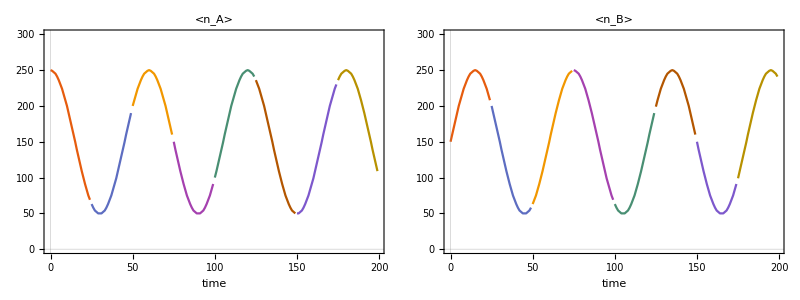

```mathematica
fmhA={};
fmhB={};
Do[
hA=Transpose[Import[dir<>"/moments/hA_"<>IntegerString[nOpt1,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
hB=Transpose[Import[dir<>"/moments/hB_"<>IntegerString[nOpt1,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
Do[
hA[[k]]=Transpose[{Table[(i-1)*25+j-1,{j,1,25}],hA[[k]]}];
hB[[k]]=Transpose[{Table[(i-1)*25+j-1,{j,1,25}],hB[[k]]}];
,{k,1,2}];
AppendTo[fmhA,hA];
AppendTo[fmhB,hB];
,{i,1,8}];
fmhA=Flatten[fmhA,1];
fmhB=Flatten[fmhB,1];
plt=Grid[{
{ListLinePlot[fmhA[[{1,3,5,7,9,11,13,15}]],PlotRange->{{0,200-1},momsMinMax["hA"]},FrameLabel->{"time"},PlotLabel->"<n_A>"],
ListLinePlot[fmhB[[{1,3,5,7,9,11,13,15}]],PlotRange->{{0,200-1},momsMinMax["hB"]},FrameLabel->{"time"},PlotLabel->"<n_B>"]
}
}]
```

```mathematica
Export["/Users/oernst/Research/cnl/multiscale/*doi_boltzmann_eric_dkl/hidden_layers/figures/circular_split.pdf",plt];
```

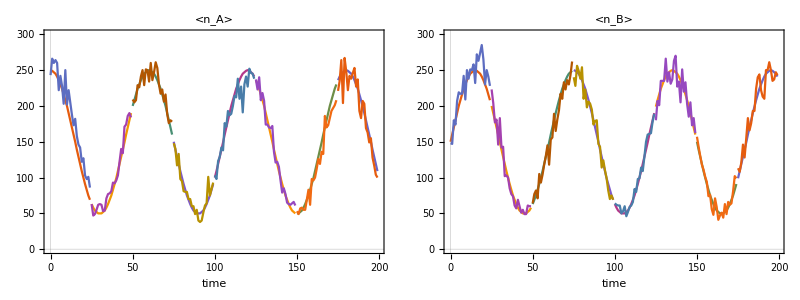

```mathematica
plt2=Grid[{
{ListLinePlot[fmhA,PlotRange->{{0,200-1},momsMinMax["hA"]},FrameLabel->{"time"},PlotLabel->"<n_A>"],
ListLinePlot[fmhB,PlotRange->{{0,200-1},momsMinMax["hB"]},FrameLabel->{"time"},PlotLabel->"<n_B>"]
}
}]
```

```mathematica
Export["/Users/oernst/Research/cnl/multiscale/*doi_boltzmann_eric_dkl/hidden_layers/figures/circular_split_learned.pdf",plt2];
```

/Users/oernst/Research/cnl/multiscale/*doi_boltzmann_eric_dkl/hidden_layers/figures/circular_split_learned.pdf

Nu dynamic

```mathematica
Manipulate[
Quiet[Check[
fmnuA={};
fmnuB={};
fmnuC={};
Do[
nuA=Flatten[Import[dir<>"/ixn_params/hA_"<>IntegerString[iOpt,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
nuB=Flatten[Import[dir<>"/ixn_params/hB_"<>IntegerString[iOpt,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
nuC=Flatten[Import[dir<>"/ixn_params/hC_"<>IntegerString[iOpt,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
AppendTo[fmnuA,nuA];
AppendTo[fmnuB,nuB];
AppendTo[fmnuC,nuC];
,{i,1,8}];
ListPlot[Table[Transpose[{fmnuA[[i]],fmnuB[[i]]}],{i,1,8}],PlotRange->All]/.Point->Line
,
(* Fail *)
"Fail"
]]
,{iOpt,0,nOpt-1,1}]
```

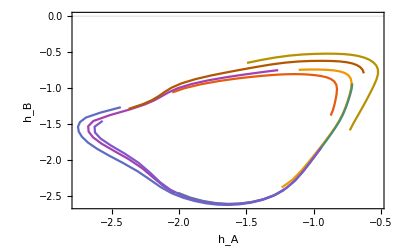

```mathematica
fmnuA={};
fmnuB={};
fmnuC={};
Do[
nuA=Flatten[Import[dir<>"/ixn_params/hA_"<>IntegerString[nOpt1,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
nuB=Flatten[Import[dir<>"/ixn_params/hB_"<>IntegerString[nOpt1,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
nuC=Flatten[Import[dir<>"/ixn_params/hC_"<>IntegerString[nOpt1,10,4]<>"_"<>IntegerString[i,10,4]<>".txt","Table"]];
AppendTo[fmnuA,nuA];
AppendTo[fmnuB,nuB];
AppendTo[fmnuC,nuC];
,{i,1,8}];
plt3=ListPlot[Table[Transpose[{fmnuA[[i]],fmnuB[[i]]}],{i,1,8}],PlotRange->All,FrameLabel->{"h_A","h_B"}]/.Point->Line
```

```mathematica
Export["/Users/oernst/Research/cnl/multiscale/*doi_boltzmann_eric_dkl/hidden_layers/figures/circular_split_ixn_params.pdf",plt3];
```

Test

```mathematica
testA=Flatten[Import["test_split/hA_0000.txt","Table"]];
testB=Flatten[Import["test_split/hB_0000.txt","Table"]];
```

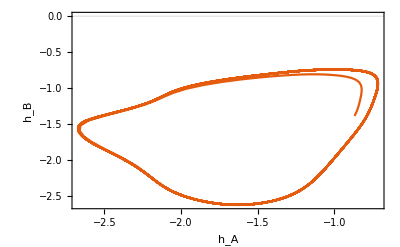

```mathematica
plt4=ListLinePlot[Transpose[{testA,testB}],FrameLabel->{"h_A","h_B"}]
```

```mathematica
Export["/Users/oernst/Research/cnl/multiscale/*doi_boltzmann_eric_dkl/hidden_layers/figures/circular_split_ixn_params_evolved.pdf",plt4];
```